max(-s/2,x-r)-min((3 s)/2,r+x)+2 s

Piecewise[{{2 s-2 r, 2 r<s+2 x∧2 (r+x)<3 s}, {-r+(3 s)/2-x, 2 r≥s+2 x∧2 (r+x)<3 s}, {-r+s/2+x, 2 r<s+2 x∧2 (r+x)≥3 s}}]

max((3 s)/2,r+x)-min(-s/2,x-r)-2 s

Piecewise[{{2 (r-s), 2 r>s+2 x∧2 (r+x)>3 s}, {r-s/2-x, 2 r>s+2 x∧2 (r+x)≤3 s}, {r-(3 s)/2+x, 2 r≤s+2 x∧2 (r+x)>3 s}}]

Piecewise[{{2 s-2 r, 2 r<s}, {s, 2 r==s}, {(2 r-3 s)^2/(4 s), (2 r<3 s∧r≥s)∨(r<s∧2 r>s)}}]

Piecewise[{{2 (r-s), 2 r≥3 s}, {s/4, r==s}, {(s-2 r)^2/(4 s), 2 r<3 s∧((2 r>s∧r<s)∨r>s)}}]

-Graphics3D-

-Graphics3D-

-Graphics3D-

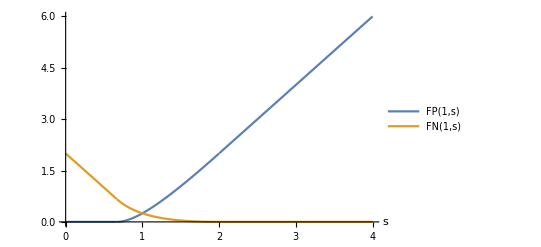

```mathematica
(*Assumptions*)
$Assumptions=Element[{r,s,x},Reals]&&r>0&&s>0&&x≥0&&x≤s;

(*Definitions*)
fp[x_,r_,s_]:=2s-(Min[(3/2)s,x+r]-Max[-s/2,x-r]);
fn[x_,r_,s_]:=(Max[(3/2)s,x+r]-Min[-s/2,x-r])-2s;
p[x_]:=1/s;
FP[r_,s_]=Integrate[fp[x,r,s]p[x],{x,0,s}];
FN[r_,s_]=Integrate[fn[x,r,s]p[x],{x,0,s}];

(*Prints*)
fp[x,r,s]//TraditionalForm
PiecewiseExpand[fp[x,r,s]] //Simplify//TraditionalForm
fn[x,r,s]//TraditionalForm
PiecewiseExpand[fn[x,r,s]] //Simplify // TraditionalForm
FP[r,s]//FullSimplify//TraditionalForm
FN[r,s]//FullSimplify//TraditionalForm

(*Plots*)
Plot3D[fp[x,1,s],{s,0,5},{x,0,s},AxesLabel->Automatic]
Plot3D[fn[x,1,s],{s,0,5},{x,0,s},AxesLabel->Automatic]
Plot3D[{fp[x,1,s],fn[x,1,s]},{s,0,5},{x,0,s},AxesLabel->Automatic,PlotLegends->"Expressions"]

Plot[{FP[1,s],FN[1,s]},{s,0,4},AxesLabel->Automatic,PlotLegends->"Expressions"]
```